```mathematica
ClearAll["Global`*"]
```

The Jacobian at the internal steady state

[Note - I added a negative sign to recovery rates!!! Otherwise the rate is negative]

Plotting a distribution of Starvation rates vs. Hopf boundaries vs. TC boundaries as a function of increasing body mass and increasing parameter noise

Needs to be redone by calculating distance between Hopf curve and value vs. TC curve vs. value

```mathematica
TCMHfunc[ts_,M_,B0_,Bm_,Em_,η_,η2_,λ0_,ef_,γ_,ζ_,f0_,mm0_] :=(
Jac = ({{ts*(λ-(1-R) σ), ts*R ρ, ts*H ρ+F σ}, {ts*(1-R) σ, ts*(-μ-R ρ), ts*(-H ρ-F σ)}, {ts*(-m R), ts*(-R ρ), ts*(-F m+(1-R) α-R α-H ρ)}});
Rstar = (μ (-λ+σ))/(λ ρ+μ σ);
Hstar = (α λ^2 (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));
Fstar = (α λ μ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));

JacSpecSol = FullSimplify[Jac/.{R->Rstar, H->Hstar, F->Fstar}];
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,σ];
CPG = CharacteristicPolynomial[JacSpecSol,L];
CPGL = CoefficientList[CPG,L];
Sylv = {{CPGL[[2]],CPGL[[1]]},{CPGL[[4]],CPGL[[3]]}} ;
HopfAnalytic = Solve[Det[Sylv]==0,σ];


growth =N[ts* λ0*M^η2];
starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])];
mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])];
recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])];
maintenance = ts*ef*B0*M^η;
resourcegrowth = ts*0.5;

TC = N[growth];
ValueSigma = N[starvation];
Hopf = N[HopfAnalytic/.{λ->growth,ρ->recovery,μ->mortality,m->maintenance,α->resourcegrowth}];
{TC,ValueSigma,Re[(σ/.Hopf)[[2]]]}
)
```

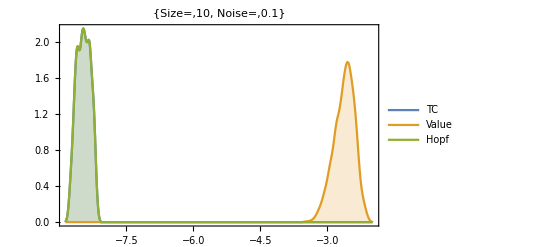
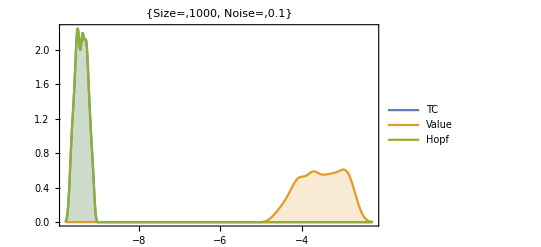
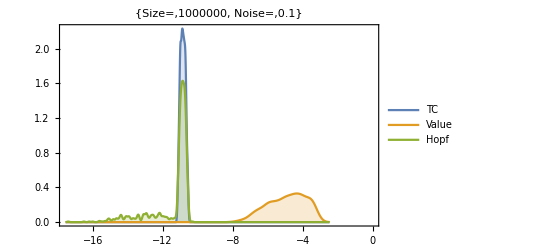
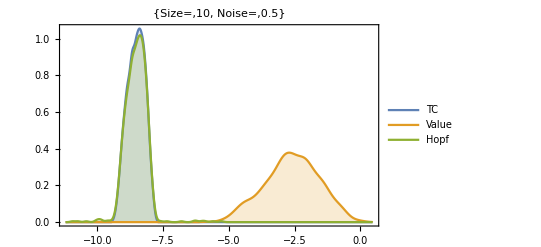
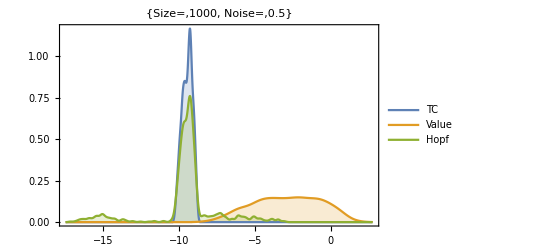
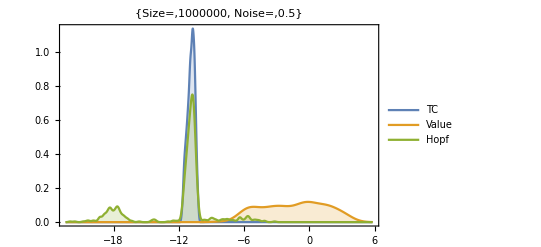

```mathematica
Table[
Table[
SigmaOutput=ParallelTable[
TCMHfunc[
(*ts*)1000,
(*M*)10^(y+RandomReal[{-0.5,0.5}]),
(*B0*)1.9*10^(-2)*(1+RandomReal[{-noise,noise}]),
(*Bm*)0.0245*(1+RandomReal[{-noise,noise}]),
(*Em*)21.39/2*1000(*J/gram*)*(1+RandomReal[{-noise,noise}]),
(*η*)3/4*(1+RandomReal[{-0,0}]),
(*η2*)-0.206*(1+RandomReal[{-0,0}]),
(*λ0*)3.3879*10^(-7)*(1+RandomReal[{-noise,noise}]),
(*ef*)0.01,
(*γ*)1.19*(1+RandomReal[{-noise,noise}]),
(*ζ*)1.01*(1+RandomReal[{-noise,noise}]),
(*f0*)0.0202*(1+RandomReal[{-noise,noise}]),
(*mm0*)0.324*(1+RandomReal[{-noise,noise}])
],{1000}];
SmoothHistogram[{Log[SigmaOutput[[All,1]]],Log[SigmaOutput[[All,2]]],Log[SigmaOutput[[All,3]]]},PlotLegends->{"TC","Value","Hopf"},Filling->Bottom,Frame->True,PlotLabel->{"Size=",10^y,"  Noise=",noise}],
{y,{1,3,6}}],{noise,{0.1,0.5}}]
```

Plotting vital rates as a function of Body Mass

```mathematica
Ratesfunc[ts_,M_,B0_,Bm_,Em_,η_,η2_,λ0_,ef_,γ_,ζ_,f0_,mm0_] :=(

growth =N[ts* λ0*M^η2];
starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])];
mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])];
recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])];
maintenance = ts*ef*B0*M^η;
resourcegrowth = ts*0.5;

{growth,starvation,mortality,recovery,maintenance,resourcegrowth}
)
```

```mathematica
RatesByMass =
Table[
With[{noise=0.01},
R=Ratesfunc[
(*ts*)1000,
(*M*)Mass=10^(y+RandomReal[{-0.5,0.5}]),
(*B0*)1.9*10^(-2)*(1+RandomReal[{-noise,noise}]),
(*Bm*)0.0245*(1+RandomReal[{-noise,noise}]),
(*Em*)21.39/2*1000(*J/gram*)*(1+RandomReal[{-noise,noise}]),
(*η*)3/4*(1+RandomReal[{-noise,noise}]),
(*η2*)-0.206*(1+RandomReal[{-noise,noise}]),
(*λ0*)3.3879*10^(-7)*(1+RandomReal[{-noise,noise}]),
(*ef*)0.000001,
(*γ*)1.19*(1+RandomReal[{-noise,noise}]),
(*ζ*)1.01*(1+RandomReal[{-noise,noise}]),
(*f0*)0.0202*(1+RandomReal[{-noise,noise}]),
(*mm0*)0.324*(1+RandomReal[{-noise,noise}])
]];
{Mass,R},
{y,1,6,0.01}];
```

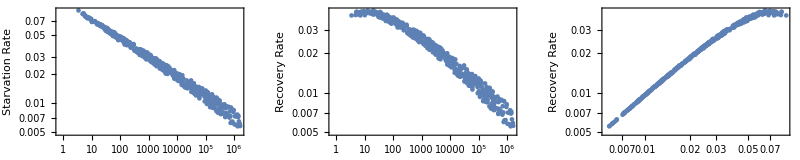

```mathematica
RatesPlot=GraphicsGrid[{{
ListLogLogPlot[Transpose[{RatesByMass[[All,1]],RatesByMass[[All,2]][[All,2]]}],Frame->True,FrameLabel->{"Mass","Starvation Rate"}],
ListLogLogPlot[Transpose[{RatesByMass[[All,1]],RatesByMass[[All,2]][[All,4]]}],Frame->True,FrameLabel->{"Mass","Recovery Rate"}],
ListLogLogPlot[Transpose[{RatesByMass[[All,2]][[All,2]],RatesByMass[[All,2]][[All,4]]}],Frame->True,FrameLabel->{"Starvation Rate","Recovery Rate"}]
}},ImageSize->800]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_Rates.pdf",RatesPlot,"PDF",ImageResolution->300]
```

Imaging the Hopf Bifurcation lines

```mathematica
HopfLinefunc[x_] :=(
noise=x[[1]];
ts=x[[2]];
M=x[[3]];
B0=x[[4]];
Bm=x[[5]];
Em=x[[6]];
η=x[[7]];
η2=x[[8]];
λ0=x[[9]];
ef=x[[10]];
γ=x[[11]];
ζ=x[[12]];
f0=x[[13]];
mm0=x[[14]];
Jac = ({{ts*(λ-(1-R) σ), ts*R ρ, ts*H ρ+F σ}, {ts*(1-R) σ, ts*(-μ-R ρ), ts*(-H ρ-F σ)}, {ts*(-m R), ts*(-R ρ), ts*(-F m+(1-R) α-R α-H ρ)}});
Rstar = (μ (-λ+σ))/(λ ρ+μ σ);
Hstar = (α λ^2 (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));
Fstar = (α λ μ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));

JacSpecSol = FullSimplify[Jac/.{R->Rstar, H->Hstar, F->Fstar}];
(*SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,σ]*);
CPG = CharacteristicPolynomial[JacSpecSol,L];
CPGL = CoefficientList[CPG,L];
Sylv = {{CPGL[[2]],CPGL[[1]]},{CPGL[[4]],CPGL[[3]]}} ;
HopfAnalytic = Solve[Det[Sylv]==0,ρ];


growth =N[ts* λ0*M^η2]*(1+RandomReal[{-noise,noise}]);
starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])]*(1+ RandomReal[{-noise,noise}]);
mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])]*(1+RandomReal[{-noise,noise}]);
recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
maintenance = (ts*ef*B0*M^η)*(1+RandomReal[{-noise,noise}]);
resourcegrowth = ts*0.5*(1 + RandomReal[{-noise,noise}]);
(*Replace everything except rho and sigma to build the curve*)
(*HopfSol = HopfAnalytic/.{λ->growth,μ->mortality,m->maintenance,α->resourcegrowth};*)
sigvalues = RecurrenceTable[{sig[n+1] == sig[n]+1/2sig[n],sig[1]==0.0000001},sig,{n,1,55}];
HopfSol = ParallelTable[{sig,Re[N[ρ/.(HopfAnalytic/.{λ->growth,μ->mortality,m->maintenance,α->resourcegrowth,σ->sig})]]},{sig,sigvalues}];

out = {growth,HopfSol,starvation,recovery}
)
```

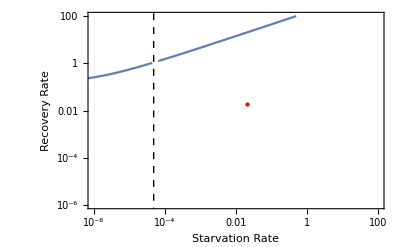

```mathematica
parameters = {
(*noise*) 0.1,
(*ts*)1000,
(*M*)10^(y+RandomReal[{-0.05,0.05}]),
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.00001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324
};
With[{y=1},
Curve = HopfLinefunc[parameters];
Show[{
(*LogLogPlot[Curve[[2]],{σ,0.000001,100},PlotRange->{{0.000001,100},{0.000001,100}},Frame->True,FrameLabel->{"Starvation Rate","Recovery Rate"}]*)

ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,1]]}],PlotRange->{{0.000001,100},{0.000001,100}},Frame->True,FrameLabel->{"Starvation Rate","Recovery Rate"},Joined->True],
ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,2]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True],
ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,3]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True],
(*ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,4]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True],*)

Graphics[{Dashed,Line[{{Log@Curve[[1]],Log@0.0000001},{Log@Curve[[1]],1000}}]}],
Graphics[{Red,PointSize[Medium],Point[{Re[Log@Curve[[3]]],Re[Log@Curve[[4]]]}]}]
}]
]
```

With replications

```mathematica
reps = 25;
Remove[y];
parameters={
(*noise*) 0.3,
(*ts*)1000,
(*M*)10^(y),
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.000001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324
};

repdataSmall = Table[
HopfLinefunc[parameters/.y->0+RandomReal[{-0.05,0.05}]],
{reps}];
repdataLarge = Table[
HopfLinefunc[parameters/.y->6+RandomReal[{-0.05,0.05}]],
{reps}];
```

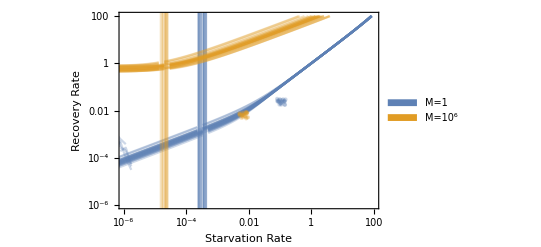

```mathematica
Opac = 0.3;
DataHopfPlot = 
Legended[
Show[
Table[
Show[{
Curve = repdataSmall[[i]];

(*LogLogPlot[Curve[[2]],{σ,0.000001,100},PlotRange->{{0.000001,100},{0.000001,100}},Frame->True,FrameLabel->{"Starvation Rate","Recovery Rate"}]*)

ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,1]]}],PlotRange->{{0.000001,100},{0.000001,100}},Frame->True,FrameLabel->{"Starvation Rate","Recovery Rate"},Joined->True,PlotStyle->Directive[Opacity[Opac]],AxesOrigin->{0,0}],
ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,2]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True,PlotStyle->Directive[Opacity[Opac]]],
ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,3]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True,PlotStyle->Directive[Opacity[Opac]]],
(*ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,4]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True],*)

Graphics[{ColorData[97,1],Opacity[Opac],Line[{{Log@Curve[[1]],Log@0.0000001},{Log@Curve[[1]],1000}}]}],
Graphics[{ColorData[97,1],PointSize[Medium],Opacity[Opac],Point[{Re[Log@Curve[[3]]],Re[Log@Curve[[4]]]}]}]
}],
{i,1,reps,1}],
Table[
Show[{
Curve = repdataLarge[[i]];

(*LogLogPlot[Curve[[2]],{σ,0.000001,100},PlotRange->{{0.000001,100},{0.000001,100}},Frame->True,FrameLabel->{"Starvation Rate","Recovery Rate"}]*)

ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,1]]}],PlotRange->{{0.000001,100},{0.000001,100}},Frame->True,FrameLabel->{"Starvation Rate","Recovery Rate"},Joined->True,PlotStyle->Directive[{ColorData[97,2],Opacity[Opac]}]],
ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,2]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True,PlotStyle->Directive[{ColorData[97,2],Opacity[Opac]}]],
ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,3]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True,PlotStyle->Directive[{ColorData[97,2],Opacity[Opac]}]],
(*ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,4]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True],*)

Graphics[{ColorData[97,2],Opacity[0.15],Line[{{Log@Curve[[1]],Log@0.0000001},{Log@Curve[[1]],1000}}]}],
Graphics[{ColorData[97,2],PointSize[Medium],Opacity[Opac],Point[{Re[Log@Curve[[3]]],Re[Log@Curve[[4]]]}]}]
}],
{i,1,reps,1}]
],SwatchLegend[{ColorData[97,1],ColorData[97,2]},{"M=1","M=10^6"}]]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_DataHopf.pdf",DataHopfPlot,"PDF",ImageResolution->300]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_DataHopf.pdf

Plot single parameter values across a range of body sizes

```mathematica
Remove[y];
parameters={
(*noise*) 0,
(*ts*)1000,
(*M*)10^(y),
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.000001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324
};
massData = Table[
HopfLinefunc[parameters/.y->i],
{i,1,6,0.25}];
```

```mathematica
MassListPlot = Table[
Massexponent = Table[i,{i,1,6,0.25}];
Show[{
Curve = massData[[i]];
Opac=1;
(*LogLogPlot[Curve[[2]],{σ,0.000001,100},PlotRange->{{0.000001,100},{0.000001,100}},Frame->True,FrameLabel->{"Starvation Rate","Recovery Rate"}]*)
ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,1]]}],PlotRange->{{0.000001,100},{0.000001,100}},Frame->True,FrameLabel->{"Starvation Rate","Recovery Rate"},Joined->True,PlotStyle->Directive[Opacity[Opac]],AxesOrigin->{0,0},PlotLabel->Round[10^Massexponent[[i]],1]],
ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,2]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True,PlotStyle->Directive[Opacity[Opac]]],
ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,3]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True,PlotStyle->Directive[Opacity[Opac]]],
(*ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,4]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True],*)

Graphics[{ColorData[97,1],Opacity[Opac],Line[{{Log@Curve[[1]],Log@0.0000001},{Log@Curve[[1]],1000}}]}],
Graphics[{ColorData[97,1],PointSize[Medium],Opacity[Opac],Point[{Re[Log@Curve[[3]]],Re[Log@Curve[[4]]]}]}]
}],
{i,1,Length[massData],1}];
```

```mathematica
MassAnimation=ListAnimate[MassListPlot,ControlPlacement->False]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/mov_bodysize.mov",MassAnimation]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/mov_bodysize.mov

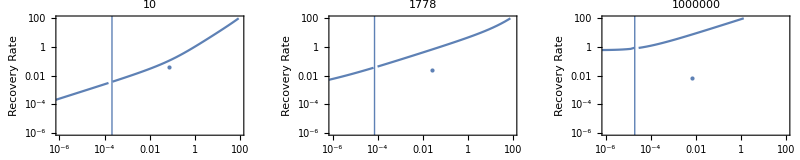

```mathematica
GraphicsGrid[{{MassListPlot[[1]],MassListPlot[[10]],MassListPlot[[21]]}},ImageSize->800]
```

```mathematica
Length[MassListPlot]
```

21

```mathematica
Round[10.3425,1]
```

10